## CSS expansion in Mellin Space (Bozzi et. al)

## Analytical expansion

Before running this notebook, create a folder named datfiles in the same directory where this notebook is located.

```mathematica
SetDirectory[NotebookDirectory[]];
```

#### Various Definitions

```mathematica
γ[i_,j_]:=Subscript[γ0,StringJoin[ToString/@{i,j}]];
γn[i_,j_]:=Subscript[γ1,StringJoin[ToString/@{i,j}]];
C1[i_,j_]:=Subscript[C1,StringJoin[ToString/@{i,j}]];
```

#### Coefficient functions

```mathematica
C1gg=0;C1gq[nn_]:=CF/(2(nn+1));hh1gg=1/2(11+3 π^2);
```

#### Anomalous Dimensions

```mathematica
(*One Loop Anomalous Dimensions [From Bonvini thesis]*)
γNqq[nn_]:=CF/2(3/2-1/(nn+1)-1/(nn+2)-2PolyGamma[nn+2]-2EulerGamma);
γNqg[nn_]:=nf/2(1/(nn+1)-2/(nn+2)+2/(nn+3));
γNgq[nn_]:=CF/2(2/nn-2/(nn+1)+1/(nn+2));
γNgg[nn_]:=CA(1/nn-1/(nn+1)+1/(nn+2)-1/(nn+3)-PolyGamma[nn+2]-EulerGamma)+β0;
```

```mathematica
(*One Loop Anomalous Dimensions [From Vogt paper]*)
Sp[m_,M_]:=Sum[i^-m,{i,1,M}];
γNggV[nn_]:=CA(Sp[1,nn-2]-2Sp[1,nn-1]-2Sp[1,nn+1]+Sp[1,nn+2]+3Sp[1,nn])+β0;
```

```mathematica
(*Numerical One Loop Anomalous Dimensions*)
γN0gg[n_?NumericQ]:=NIntegrate[x^(n-1) CA(1/x+x-x^2-2)+(x^(n-1)-1)CA/(1-x),{x,0,1},WorkingPrecision->12,AccuracyGoal->12,MaxRecursion->20]+β0;
```

In order to compare γNgg with γN0gg (or with the threshold), it should be noted that γN0gg is shifted by 1, therefore, the correct comparison for a given N is γN0gg(N)=γNgg(N-1).

```mathematica
(*Two Loops Anomalous Dimension [Mellin form can only be computed numerically]*)
δgg=-2/3 nf+27/4 Zeta[3];
sp1gg[x_]:=1/(1-x)(16.75-(5nf)/6-3/4 π^2);
sp2gg[x_]:=1/(72x(x^2-1))((-1+x) (2 nf (1+x) (-61+x (-9+x (-9+109 x)))+9 x (-(1+x) (25+109 x)+6 π^2 (3+2 x (2+x+x^2))))-12 x (2 nf (-1+x) (1+x)^2+27 (1+x-x^2)^2) Log[x]^2+6 Log[x] (108 (1+x) (1+(-1+x) x)^2 Log[1-x]+(-1+x) (-x (1+x) (225+99 x (-1+4 x)+2 nf (9+13 x))+108 (1+x+x^2)^2 Log[1+x]))+648 (-1+x) (1+x+x^2)^2 PolyLog[2,-x]);
γmgg[n_?NumericQ]:=NIntegrate[x^(n-1)sp2gg[x]+(x^(n-1)-1)sp1gg[x],{x,0,1}]+δgg;
```

#### Large-N limits of the Anomalous Dimensions:

```mathematica
γgqLargeN=0;
γqgLargeN=0;
γggLargeN=-CA(LN+EulerGamma);(*LN=Log[n]*)
```

#### H functions (contain the constant terms when pT→0)

```mathematica
H1[a_,b_]:=KroneckerDelta[g,a]KroneckerDelta[g,b](h1g-(B1+1/2 B1 LQ)LQ-pc β0 LR)+KroneckerDelta[g,a]C1[g,b]+KroneckerDelta[g,b]C1[g,a]+(KroneckerDelta[g,a]γ[g,b]+KroneckerDelta[g,b]γ[g,a])(LF-LQ);
H2[a_,b_]:=0;
```

#### Σ functions (contain the singular terms when pT→0)

```mathematica
Σ12[a_,b_]:=-A1/2 KroneckerDelta[g,a]KroneckerDelta[g,b];
Σ11[a_,b_]:=-(KroneckerDelta[g,a]KroneckerDelta[g,b](B1+A1 LQ)+KroneckerDelta[g,a]γ[g,b]+KroneckerDelta[g,b]γ[g,a]);
Σ24[a_,b_]:=(A1)^2/8 KroneckerDelta[g,a]KroneckerDelta[g,b];
Σ23[a_,b_]:=-A1(1/3 β0 KroneckerDelta[g,a]KroneckerDelta[g,b]+1/2 Σ11[a,b]);
ξ[m_,n_,a_,b_]:=Σ11[m,n](KroneckerDelta[m,a]γ[n,b]+KroneckerDelta[n,b]γ[m,a]);
Σ22[a_,b_]:=-A1/2(H1[a,b]-β0 KroneckerDelta[g,a]KroneckerDelta[g,b](LR-LQ))-1/2(A2 KroneckerDelta[g,a] KroneckerDelta[g,b]+(B1+A1 LQ-β0)Σ11[a,b])-1/2(ξ[g,g,a,b]+ξ[g,q,a,b]+ξ[q,g,a,b]+ξ[q,q,a,b]);
χ[m_,n_,a_,b_]:=H1[m,n](KroneckerDelta[m,a]KroneckerDelta[n,b](B1+A1 LQ)+KroneckerDelta[m,a]γ[n,b]+KroneckerDelta[n,b]γ[m,a]);
Σ21[a_,b_]:=Σ11[a,b]β0(LQ-LR)-(χ[g,g,a,b]+χ[g,q,a,b]+χ[q,g,a,b]+χ[q,q,a,b])-(KroneckerDelta[g,a]KroneckerDelta[g,b](B2+A2 LQ)-β0(KroneckerDelta[g,a]C1[g,b]+KroneckerDelta[g,b]C1[g,a]+KroneckerDelta[g,a]γn[g,b]+KroneckerDelta[g,b]γn[g,a]));
```

#### Fourier Inverse of Log(χ) where χ=1+b^2 Q^2/b0^2:

```mathematica
IC1[pt_,mH_]:=-b0/x BesselK[1,b0 x]/.{x-> pt/mH,b0-> 2 Exp[-EulerGamma]};
IC2[pt_,mH_]:=(2 b0)/x(BesselK[1, b0 x]Log[x]-Derivative[1,0][BesselK][1,b0 x])/.{x-> pt/mH,b0-> 2 Exp[-EulerGamma]};
IC3[pt_,mH_]:=-(3 b0)/x(BesselK[1, b0 x](Log[x]^2-Zeta[2])-2 Derivative[1,0][BesselK][1,b0 x]Log[x]+Derivative[2,0][BesselK][1,b0 x])/.{x-> pt/mH,b0-> 2 Exp[-EulerGamma]};
IC4[pt_,mH_]:=(4b0)/x(BesselK[1, b0 x](Log[x]^3-3 Zeta[2]Log[x]+2Zeta[3])-3 Derivative[1,0][BesselK][1,b0 x](Log[x]^2-Zeta[2])+3 Derivative[2,0][BesselK][1,b0 x]Log[x]-Derivative[3,0][BesselK][1,b0 x])/.{x-> pt/mH,b0-> 2 Exp[-EulerGamma]};
```

#### Fourier Inverse of Log(χ) where χ=b^2 Q^2/b0^2:

```mathematica
FC1[pt_,mH_]:=-1/x^2/.{x-> pt/mH};
FC2[pt_,mH_]:=-2/x^2 Log[1/x^2]/.{x-> pt/mH};
FC3[pt_,mH_]:=-3/x^2 Log[1/x^2]^2/.{x-> pt/mH};
FC4[pt_,mH_]:=-4/x^2(Log[1/x^2]^3-4Zeta[3])/.{x-> pt/mH};
```

LO contribution (terms only proportional to αs)

Here, we are only interested in the LO contribution at small-pt (pt→0), therefore neglecting all the constant terms in the expansion.

#### Analytical expression of the coefficients:

```mathematica
{Σ12[g,g],Σ11[g,g]/.{B1-> -2β0}}(*Coefficients of {LC2,LC1}*)
```

{-A1/2,-A1 LQ+2 β0-2 γ0_gg}

#### LO terms:

```mathematica
(*Normalized cross-section, ie divided by σ0*)
dσLO[a_,b_]:=Σ12[a,b] LC2+Σ11[a,b] LC1(*+H1[a,b]*)/.{KroneckerDelta[c_,d_]:> If[c===d,1,0]} ;(*αsp=αs/π*)
```

```mathematica
Collect[dσLO[g,g],{LC2,LC1}]
```

-(A1 LC2)/2+LC1 (-B1-A1 LQ-2 γ0_gg)

Since we are mainly interested in the pt-enhanced terms that are not multiplied by ln(N), as they are already contained in the threshold resummation, we can get rid of all the N-dependence which are contained in the Anomalous Dimensions.

```mathematica
dσLOptNoLogN=Collect[dσLO[g,g],{LC2,LC1}]/.{Subscript[γ0,StringJoin[ToString/@{g,g}]]-> 0,Subscript[γ0,StringJoin[ToString/@{g,q}]]-> 0,Subscript[γ0,StringJoin[ToString/@{q,g}]]-> 0,Subscript[γ1,StringJoin[ToString/@{g,g}]]-> 0}
```

-(A1 LC2)/2+LC1 (-B1-A1 LQ)

NLO contribution (terms only proportional to αs^2)

Similarly, here, we are only interested in the LO contribution at small-pt (pt→0), therefore neglecting all the constant terms in the expansion.

#### Analytical expression of the coefficients:

```mathematica
{Σ24[g,g],Σ23[g,g]}/.{KroneckerDelta[c_,d_]:> If[c===d,1,0],B1-> -2β0}(*Coefficients of {LC4,LC3}*)
```

{A1^2/8,-A1 (β0/3+1/2 (-A1 LQ+2 β0-2 γ0_gg))}

```mathematica
{Σ22[g,g],Σ21[g,g]}/.{KroneckerDelta[c_,d_]:> If[c===d,1,0],B1-> -2β0}(*Coefficients of {LC2,LC1}*)
```

{1/2 (-A2-(A1 LQ-3 β0) (-A1 LQ+2 β0-2 γ0_gg))-1/2 A1 (h1g-(-LQ+LR) β0-LR pc β0-LQ (-2 β0-LQ β0)+2 C1_gg+2 (LF-LQ) γ0_gg)+1/2 (-2 (-A1 LQ+2 β0-2 γ0_gg) γ0_gg+2 γ0_gq γ0_qg),-B2-A2 LQ+(LQ-LR) β0 (-A1 LQ+2 β0-2 γ0_gg)-(A1 LQ-2 β0+2 γ0_gg) (h1g-LR pc β0-LQ (-2 β0-LQ β0)+2 C1_gg+2 (LF-LQ) γ0_gg)-2 (C1_gq+(LF-LQ) γ0_gq) γ0_qg+β0 (2 C1_gg+2 γ1_gg)}

#### NLO terms:

```mathematica
(*Normalized cross-section, ie divided by σ0*)
dσNLO[a_,b_]:=Σ24[a,b] LC4+Σ23[a,b] LC3+Σ22[a,b] LC2+Σ21[a,b]LC1(*+H2[a,b]*)/.{KroneckerDelta[c_,d_]:> If[c===d,1,0]} ;(*αsp=αs/π*)
```

```mathematica
Collect[dσNLO[g,g]/.{LR-> 0,LF-> 0,LQ-> 0},{LC4,LC3,LC2,LC1}]
```

(A1^2 LC4)/8-A1 LC3 (β0/3+1/2 (-B1-2 γ0_gg))+LC2 (-1/2 A1 (h1g+2 C1_gg)+1/2 (-A2-(B1-β0) (-B1-2 γ0_gg))+1/2 (-2 (-B1-2 γ0_gg) γ0_gg+2 γ0_gq γ0_qg))+LC1 (-B2-(h1g+2 C1_gg) (B1+2 γ0_gg)-2 C1_gq γ0_qg+β0 (2 C1_gg+2 γ1_gg))

As before, since we are mainly interested in the pt-enhanced terms that are not multiplied by ln(N), as they are already contained in the threshold resummation, we can get rid of all the N-dependence which are contained in the Anomalous Dimensions.

```mathematica
dσNLOptNoLogN=Collect[dσNLO[g,g],{LC4,LC3,LC2,LC1}]/.{Subscript[γ0,StringJoin[ToString/@{g,g}]]-> 0,Subscript[γ0,StringJoin[ToString/@{g,q}]]-> 0,Subscript[γ0,StringJoin[ToString/@{q,g}]]-> 0,Subscript[γ1,StringJoin[ToString/@{g,g}]]-> 0}
```

(A1^2 LC4)/8-A1 LC3 (1/2 (-B1-A1 LQ)+β0/3)+LC1 (-B2-A2 LQ+(-B1-A1 LQ) (LQ-LR) β0+2 β0 C1_gg-(B1+A1 LQ) (h1g-LQ (B1+(B1 LQ)/2)-LR pc β0+2 C1_gg))+LC2 (1/2 (-A2-(-B1-A1 LQ) (B1+A1 LQ-β0))-1/2 A1 (h1g-LQ (B1+(B1 LQ)/2)-(-LQ+LR) β0-LR pc β0+2 C1_gg))

The term above is what should be supplemented to the threshold resummation at NLO.

```mathematica
(*In case LR=LF=LQ=mH*)
Collect[dσNLO[g,g],{LC4,LC3,LC2,LC1}]/.{Subscript[γ0,StringJoin[ToString/@{g,g}]]-> 0,Subscript[γ0,StringJoin[ToString/@{g,q}]]-> 0,Subscript[γ0,StringJoin[ToString/@{q,g}]]-> 0,Subscript[γ1,StringJoin[ToString/@{g,g}]]-> 0}/.{LR-> 0,LF-> 0,LQ-> 0}
```

(A1^2 LC4)/8-A1 LC3 (-B1/2+β0/3)+LC2 (1/2 (-A2+B1 (B1-β0))-1/2 A1 (h1g+2 C1_gg))+LC1 (-B2+2 β0 C1_gg-B1 (h1g+2 C1_gg))

## Numerical Checks

Here, as a proof of concept, we check that in the small-pt limit, the results of the expansion agree with the C++ implementation.

#### Physical constants

```mathematica
GF=1.166378 10^-5;GevtoPb=3.8937966 10^8; (*constants*)
nf=5; (*number of active flavours*)
CA=nc=3;CF=(nc^2-1)/(2nc); (*Casimir Operators*)
β0=1/12(11 CA-2nf);(* Beta functions [According to Bozzi's definition]*)
σ0[α_]:=(α^2 √2 GF)/(576π); (*Born level cross-section σ0*)
(*Coeff. Cusp Anomalous Dimensions*)
A1g=CA;B1g=-2β0;
A2g=CA/2(CA(67/18-Zeta[2])-5/9 nf);
B2g=1/(16 π^2)((-64/3-24 Zeta[3])CA^2+16/3 nf CA+4 nf CF)+β0 CA/π Zeta[2];
αs=0.11264;mH=125;μF=125;μR=125;Q=125;
LRR=Log[mH^2/μR^2];LFF=Log[mH^2/μF^2];LQ2=Log[mH^2/Q^2];
NN=3(*Mellin Moment*); PT=10(*pt value in GeV*);
(*The above definitions should always be the same as in the input card for C++*)
```

LO contribution (terms only proportional to αs)

```mathematica
NumΣLO[n_,pt_]:=(αs/π)(2 pt)/mH^2 (GevtoPb)σ0[αs]dσLO[g,g]/.{LC1-> FC1[pt,mH],LC2-> FC2[pt,mH]}/.{Subscript[γ0,StringJoin[ToString/@{g,g}]]-> γNgg[n-1]}/.{A1-> A1g,B1-> B1g}/.{LR-> LRR,LF->LFF,LQ-> LQ2};
```

```mathematica
cssLOaspt=Table[{pt,NumΣLO[NN,pt]},{pt,1,20,0.01}];
Export["./datfiles/cssLOaspt.dat",cssLOaspt,"Table"];
```

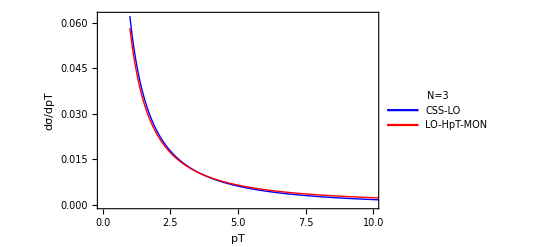

```mathematica
ListLinePlot[{Import["./datfiles/cssLOaspt.dat","Table"],Import["./datfiles/morepoints_smallpt_LO_gg_channel.dat","Table"]},Frame->True,FrameStyle->Directive[Black,12],PlotStyle->{{Thick,Blue},{Thick,Red}},PlotLegends->Placed[LineLegend[{"CSS-LO","LO-HpT-MON"},LabelStyle->{Black,10},LegendLabel->"N=3",LegendFunction->"Frame"],{0.7,0.7}],FrameLabel->{{"dσ/dpT",""},{"pT", "LO Contribution"}},PlotRange->{{0,10},All}]
```

NLO contribution (terms only proportional to αs^2)

```mathematica
NumΣNLO[n_,pt_]:=(αs/π)^2(2 pt)/mH^2 (GevtoPb)σ0[αs]dσNLO[g,g]/.{LC1-> FC1[pt,mH],LC2-> FC2[pt,mH],LC3-> FC3[pt,mH],LC4-> FC4[pt,mH]}/.{Subscript[γ0,StringJoin[ToString/@{g,g}]]-> γNgg[n-1],Subscript[γ0,StringJoin[ToString/@{g,q}]]-> γNgq[n-1],Subscript[γ0,StringJoin[ToString/@{q,g}]]-> γNqg[n-1],Subscript[γ0,StringJoin[ToString/@{q,q}]]-> γNqq[n-1],Subscript[γ1,StringJoin[ToString/@{g,g}]]-> γmgg[n]}/.{Subscript[C1,StringJoin[ToString/@{g,g}]]-> C1gg,
Subscript[C1,StringJoin[ToString/@{g,q}]]-> C1gq[n]}/.{A1-> A1g,A2-> A2g,B1-> B1g,B2-> B2g}/.{LR-> LRR,LF->LFF,LQ-> LQ2}/.h1g-> hh1gg;
```

```mathematica
cssNLOaspt=Table[{pt,NumΣNLO[NN,pt]},{pt,1,20,0.01}];
Export["./datfiles/cssNLOaspt.dat",cssNLOaspt,"Table"];
```

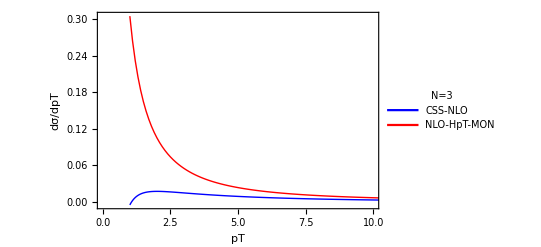

```mathematica
ListLinePlot[{Import["./datfiles/cssNLOaspt.dat","Table"],Import["./datfiles/morepoints_smallpt_NLO_without_LO.dat","Table"]},Frame->True,FrameStyle->Directive[Black,12],PlotStyle->{{Thick,Blue},{Thick,Red}},PlotLegends->Placed[LineLegend[{"CSS-NLO","NLO-HpT-MON"},LabelStyle->{Black,10},LegendLabel->"N=3",LegendFunction->"Frame"],{0.7,0.7}],FrameLabel->{{"dσ/dpT",""},{"pT", "NLO Contribution"}},PlotRange->{{0,10},All}]
```

## Check log(pt)log(N)

Here, we analytically check that the ln(pt)ln(N) that are present in the small-pt match those from the threshold.

```mathematica
Clear[A1,B1,CA,β0];
```

```mathematica
CompareThreshold={Subscript[γ0,StringJoin[ToString/@{g,q}]]-> 0,Subscript[γ0,StringJoin[ToString/@{q,g}]]-> 0,Subscript[C1,StringJoin[ToString/@{g,g}]]->0};
LptLN=Collect[dσNLO[g,g]/.{LR-> 0,LF-> 0,LQ-> 0}(*/.{B1-> -2β0}*)/.CompareThreshold,{LC4,LC3,LC2,LC1}]
```

(A1^2 LC4)/8-A1 LC3 (β0/3+1/2 (-B1-2 γ0_gg))+LC2 (-(A1 h1g)/2+1/2 (-A2-(B1-β0) (-B1-2 γ0_gg))-(-B1-2 γ0_gg) γ0_gg)+LC1 (-B2-h1g (B1+2 γ0_gg)+2 β0 γ1_gg)

```mathematica
LptLargeN=Select[LptLN//Expand,MemberQ[#,Subscript[γ0,StringJoin[ToString/@{g,g}]]|Subscript[γ0,StringJoin[ToString/@{g,g}]]^_|Subscript[γ1,StringJoin[ToString/@{g,g}]]]&]
```

-2 h1g LC1 γ0_gg+2 B1 LC2 γ0_gg+A1 LC3 γ0_gg-LC2 β0 γ0_gg+2 LC2 γ0_gg^2+2 LC1 β0 γ1_gg

```mathematica
(*Recall that the expression below is multiplied by (αs/π)^2*)
mapLC={LC1-> -1/ξp,LC2-> 2 Log[ξp]/ξp,LC3-> 3(Log[ξp])^2/ξp};
mapγgg={Subscript[γ0,StringJoin[ToString/@{g,g}]]->-CA LNb};(*LNb=Log[n γE]≠Lnb2*)
Collect[LptLargeN/.mapγgg/.mapLC,LNb]
```

(4 CA^2 LNb^2 Log[ξp])/ξp+LNb (-(2 CA h1g)/ξp-(4 B1 CA Log[ξp])/ξp+(2 CA β0 Log[ξp])/ξp-(3 A1 CA Log[ξp]^2)/ξp)-(2 β0 γ1_gg)/ξp

```mathematica
Collect[(Agth1 Log[ξp])/ξp((3 Agth1 LNb2^2)/8+LNb2 (-Bgth1/2-1/2 Agth1 Log[ξp]/2))/.{LNb2-> 2 LNb}//Expand,LNb]
```

(3 Agth1^2 LNb^2 Log[ξp])/(2 ξp)+LNb (-(Agth1 Bgth1 Log[ξp])/ξp-(Agth1^2 Log[ξp]^2)/(2 ξp))